# SelectDiscard

Separate a list into two lists based on a given condition

## Definition

This notebook was automatically generated from Definitions/SelectDiscard.

```mathematica
SelectDiscard // ClearAll;
```

### Initialization

```mathematica
$inDef = False;
$debug = True;
```

#### beginDefinition

```mathematica
beginDefinition // ClearAll;
```

```mathematica
beginDefinition // Attributes = { HoldFirst };
```

```mathematica
beginDefinition::Unfinished =
"Starting definition for `1` without ending the current one.";
```

:!CodeAnalysis::BeginBlock::

:!CodeAnalysis::Disable::SuspiciousSessionSymbol::

```mathematica
beginDefinition[ s_Symbol ] /; $debug && $inDef :=
    WithCleanup[
        $inDef = False
        ,
        Print @ TemplateApply[ beginDefinition::Unfinished, HoldForm @ s ];
        beginDefinition @ s
        ,
        $inDef = True
    ];
```

:!CodeAnalysis::EndBlock::

```mathematica
beginDefinition[ s_Symbol ] :=
    WithCleanup[ Unprotect @ s; ClearAll @ s, $inDef = True ];
```

#### endDefinition

```mathematica
endDefinition // beginDefinition;
```

```mathematica
endDefinition // Attributes = { HoldFirst };
```

```mathematica
endDefinition[ s_Symbol ] := endDefinition[ s, DownValues ];
```

```mathematica
endDefinition[ s_Symbol, None ] := $inDef = False;
```

```mathematica
endDefinition[ s_Symbol, DownValues ] :=
    WithCleanup[
        AppendTo[ DownValues @ s,
                  e: HoldPattern @ s[ ___ ] :>
                      throwInternalFailure @ HoldForm @ e
        ],
        $inDef = False
    ];
```

```mathematica
endDefinition[ s_Symbol, SubValues  ] :=
    WithCleanup[
        AppendTo[ SubValues @ s,
                  e: HoldPattern @ s[ ___ ][ ___ ] :>
                      throwInternalFailure @ HoldForm @ e
        ],
        $inDef = False
    ];
```

```mathematica
endDefinition[ s_Symbol, list_List ] :=
    endDefinition[ s, # ] & /@ list;
```

```mathematica
endDefinition // endDefinition;
```

### Messages

```mathematica
SelectDiscard::Internal =
"An unexpected error occurred. `1`";
```

```mathematica
SelectDiscard::Normal =
"Nonatomic expression expected at position 1 in `1`.";
```

```mathematica
SelectDiscard::ArgumentCount =
"SelectDiscard called with `1` arguments; between 1 and 3 arguments are expected.";
```

```mathematica
SelectDiscard::Count =
"Non-negative integer or Infinity expected at position 3 in `1`.";
```

### Argument patterns

```mathematica
$$assoc      = _Association? associationQ;
$$sparse     = _SparseArray? sparseArrayQ;
$$graph      = _Graph? graphQ;
$$normal     = _[ ___ ] | $$assoc | $$sparse;
$$selectable = $$normal | $$graph;
$$posInt     = _Integer? NonNegative;
$$count      = $$posInt | UpTo[ $$posInt ] | Infinity;
```

#### associationQ

```mathematica
associationQ // ClearAll;
associationQ // Attributes = { HoldAllComplete };
associationQ[ as_Association ] := AssociationQ @ Unevaluated @ as;
associationQ[ ___ ] := False;
```

#### sparseArrayQ

```mathematica
sparseArrayQ // ClearAll;
sparseArrayQ // Attributes = { HoldAllComplete };
sparseArrayQ[ sa_SparseArray ] := SparseArrayQ @ Unevaluated @ sa;
sparseArrayQ[ ___ ] := False;
```

#### graphQ

```mathematica
graphQ // ClearAll;
graphQ // Attributes = { HoldAllComplete };
graphQ[ gr_Graph ] := GraphQ @ Unevaluated @ gr;
graphQ[ ___ ] := False;
```

### Main definition

```mathematica
SelectDiscard[ list: $$selectable, crit_ ] :=
    catchTop @ selectDiscard[ list, crit ];
```

```mathematica
SelectDiscard[ list: $$selectable, crit_, n: $$count ] :=
    catchTop @ selectDiscard[ list, crit, n ];
```

```mathematica
SelectDiscard[ crit_ ][ list_ ] :=
    catchTop @ SelectDiscard[ Unevaluated @ list, crit ];
```

### Error cases

Wrong number of arguments:

```mathematica
SelectDiscard[ ] := catchTop @ throwFailure[ "ArgumentCount", 0 ];

SelectDiscard[ a_, b_, c_, d__ ] :=
    catchTop @ throwFailure[
        "ArgumentCount",
        Length @ HoldComplete[ a, b, c, d ]
    ];
```

First argument is atomic:

```mathematica
SelectDiscard[ expr_? atomQ, a__ ] :=
    catchTop @ throwFailure[
        "Normal",
        HoldForm @ SelectDiscard[ expr, a ]
    ];
```

Invalid count:

```mathematica
SelectDiscard[ list_, crit_, count: Except[ $$count ] ] :=
    catchTop @ throwFailure[
        "Count",
        HoldForm @ SelectDiscard[ list, crit, count ]
    ];
```

Missed something that needs to be fixed:

```mathematica
e: SelectDiscard[ _, __ ] := catchTop @ throwInternalFailure @ e;
```

### Dependencies

#### selectDiscard

```mathematica
selectDiscard // beginDefinition;
```

```mathematica
selectDiscard[ list_List, crit_ ] :=
    Lookup[ GroupBy[ Unevaluated @ list, bool @ crit ],
            { True, False },
            { }
    ];
```

```mathematica
selectDiscard[ list: $$normal, crit_ ] := {
    select[ list, crit ],
    select[ list, not @ crit ]
};
```

```mathematica
selectDiscard[ graph: $$graph, args__ ] := Enclose[
    Module[ { vertices, v1, v2, g1, g2 },
        vertices = ConfirmBy[ VertexList @ graph, ListQ ];
        { v1, v2 } = ConfirmMatch[ SelectDiscard[ vertices, args ], { _, _ } ];
        g1 = ConfirmBy[ Subgraph[ graph, v1 ], GraphQ ];
        g2 = ConfirmBy[ Subgraph[ graph, v2 ], GraphQ ];
        { g1, g2 }
    ],
    throwInternalFailure @ selectDiscard[ graph, args ] &
];
```

```mathematica
selectDiscard[ list_, crit_, Infinity | UpTo[ Infinity ] ] :=
    selectDiscard[ list, crit ];
```

```mathematica
selectDiscard[ list_, crit_, UpTo[ n: $$posInt ] ] :=
    Module[ { a, b, a1, a2 },
        { a, b } = selectDiscard[ list, crit ];
        { a1, a2 } = TakeDrop[ a, UpTo[ n ] ];
        { a1, Join[ a2, b ] }
    ];
```

```mathematica
selectDiscard[ list_, crit_, n: $$posInt ] :=
    selectDiscard[ list, crit, UpTo[ n ] ];
```

```mathematica
selectDiscard // Attributes = { HoldAllComplete };
selectDiscard // endDefinition;
```

#### bool

```mathematica
bool // beginDefinition;
bool[ crit_ ] := Function[ e, TrueQ @ crit @ e, HoldAllComplete ];
bool // endDefinition;
```

#### select

```mathematica
select // beginDefinition;
```

```mathematica
select // Attributes = { HoldAllComplete };
```

```mathematica
select[ list_, a__ ] :=
    Replace[ Select[ Unevaluated @ list, a ],
             _Select :> throwInternalFailure @ select[ list, a ]
    ];
```

```mathematica
select // endDefinition;
```

#### not

```mathematica
not // beginDefinition;
not[ crit_ ] := Function[ e, ! TrueQ @ crit @ e, HoldAllComplete ];
not // endDefinition;
```

#### atomQ

```mathematica
atomQ // ClearAll;
atomQ // Attributes = { HoldAllComplete };
atomQ[ expr_ ] := AtomQ @ Unevaluated @ expr;
atomQ[ ___   ] := False;
```

#### Error handling

##### catchTop

```mathematica
catchTop // beginDefinition;
```

```mathematica
catchTop // Attributes = { HoldFirst };
```

```mathematica
catchTop[ eval_ ] :=
    Block[ { $catching = True, $failed = False, catchTop = # & },
        Catch[ eval, $top ]
    ];
```

```mathematica
catchTop // endDefinition;
```

##### throwFailure

```mathematica
throwFailure // beginDefinition;
```

```mathematica
throwFailure // Attributes = { HoldFirst };
```

```mathematica
throwFailure[ tag_String, params___ ] :=
    throwFailure[ MessageName[ SelectDiscard, tag ], params ];
```

```mathematica
throwFailure[ msg_, args___ ] :=
    Module[ { failure },
        failure = messageFailure[ msg, Sequence @@ HoldForm /@ { args } ];
        If[ TrueQ @ $catching,
            Throw[ failure, $top ],
            failure
        ]
    ];
```

```mathematica
throwFailure // endDefinition;
```

##### messageFailure

```mathematica
messageFailure // beginDefinition;
```

```mathematica
messageFailure // Attributes = { HoldFirst };
```

```mathematica
messageFailure[ args___ ] :=
    Module[ { quiet },
        quiet = If[ TrueQ @ $failed, Quiet, Identity ];
        WithCleanup[
            quiet @ ResourceFunction[ "MessageFailure" ][ args ],
            $failed = True
        ]
    ];
```

```mathematica
messageFailure // endDefinition;
```

##### throwInternalFailure

```mathematica
throwInternalFailure // beginDefinition;
```

```mathematica
throwInternalFailure // Attributes = { HoldFirst };
```

```mathematica
throwInternalFailure[ eval_, a___ ] :=
    throwFailure[ SelectDiscard::Internal, $bugReportLink, HoldForm @ eval, a ];
```

```mathematica
throwInternalFailure // endDefinition;
```

##### $bugReportLink

```mathematica
$bugReportLink := $bugReportLink = Hyperlink[
    "Report this issue »",
    URLBuild @ <|
        "Scheme"   -> "https",
        "Domain"   -> "resources.wolframcloud.com",
        "Path"     -> { "FunctionRepository", "feedback-form" },
        "Fragment" -> "SelectDiscard"
    |>
];
```

## Documentation

### Usage

SelectDiscard[list,crit]

gives the pair {list_1,list_2} where list_1 contains all elements e_i of list for which crit[e_i] is True and list_2 contains the rest.

SelectDiscard[list,crit,n]

limits list_1 to n elements.

SelectDiscard[crit]

represents an operator form of SelectDiscard that can be applied to an expression.

### Details & Options

The list_1 can be thought of as the "selected" elements, and list_2 as the "discarded" elements.

The values e_i in list_2 do not necessarily give False for crit[e_i]; they are simply the elements not included in list_1.

The object list can have any head, not necessarily List.

When used on an Association, SelectDiscard picks out elements according to their values.

SelectDiscard can be used on SparseArray objects.

SelectDiscard[crit][list] is equivalent to SelectDiscard[list,crit].

## Examples

```mathematica
ClearAll[ "Global`*" ];
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
```

TestReportObject[…]

### Basic Examples

Separate elements that are even:

```mathematica
SelectDiscard[{1,2,4,7,6,2},EvenQ]
```

{{2,4,6,2},{1,7}}

Use a pure function to test each element:

```mathematica
SelectDiscard[{1,2,4,7,6,2},#>2&]
```

{{4,7,6},{1,2,2}}

Select only the first expression that satisfies the condition:

```mathematica
SelectDiscard[{1,2,4,7,6,2},#>2&,1]
```

{{4},{7,6,1,2,2}}

Use the operator form of SelectDiscard:

```mathematica
SelectDiscard[EvenQ][{1,2,4,7,6,2}]
```

{{2,4,6,2},{1,7}}

SelectDiscard operates on values in an Associationpaclet:ref/Association:

```mathematica
SelectDiscard[<|a->1,b->2,c->3,d->4|>,#>2&]
```

{<|c→3,d→4|>,<|a→1,b→2|>}

### Scope

SelectDiscard gives elements for which applying the criterion explicitly yields Truepaclet:ref/True in the first list and everything else in the second:

```mathematica
SelectDiscard[{1,2,4,7,x},#>2&]
```

{{4,7},{1,2,x}}

Applying the criterion to the symbolic object x does not explicitly yield Truepaclet:ref/True:

```mathematica
x>2
```

x>2

Find pairs containing x:

```mathematica
SelectDiscard[{{1,y},{2,x},{3,x},{4,z}, {5,x}},MemberQ[#,x]&]
```

{{{2,x},{3,x},{5,x}},{{1,y},{4,z}}}

Find up to 2 pairs containing x:

```mathematica
SelectDiscard[{{1,y},{2,x},{3,x},{4,z}, {5,x}},MemberQ[#,x]&,2]
```

{{{2,x},{3,x}},{{5,x},{1,y},{4,z}}}

Fewer than the requested elements may be returned:

```mathematica
SelectDiscard[{{1,y},{2,x},{3,x},{4,z}, {5,x}},MemberQ[#,z]&,2]
```

{{{4,z}},{{1,y},{2,x},{3,x},{5,x}}}

Use an operator form as selection criterion:

```mathematica
SelectDiscard[Range[10],GreaterThan[3]]
```

{{4,5,6,7,8,9,10},{1,2,3}}

Use SelectDiscard in operator form:

```mathematica
Range[10]//SelectDiscard[GreaterThan[3]]
```

{{4,5,6,7,8,9,10},{1,2,3}}

Separate arguments in Unevaluated code:

```mathematica
SelectDiscard[Unevaluated[1+2+3+4+5],OddQ]
```

{9,6}

### Generalizations & Extensions

SelectDiscard works with any head, not just Listpaclet:ref/List:

```mathematica
SelectDiscard[f[1,a,2,b,3],IntegerQ]
```

{f[1,2,3],f[a,b]}

SelectDiscard works with SparseArraypaclet:ref/SparseArray objects:

```mathematica
s=SparseArray[Table[2^i->i,{i,0,5}]]
```

SparseArray[…]

```mathematica
SelectDiscard[s,EvenQ]
```

{SparseArray[…],{1,3,5}}

The result includes a list since only one can be sparse:

```mathematica
SelectDiscard[s,OddQ]
```

{{1,3,5},SparseArray[…]}

Compare to Select:

```mathematica
Select[s,EvenQ]
```

SparseArray[…]

```mathematica
Select[s,OddQ]
```

{1,3,5}

Separate a Dataset:

```mathematica
dataset=Dataset[{
<|"a"->1,"b"->"x","c"->{1}|>,
<|"a"->2,"b"->"y","c"->{2,3}|>,
<|"a"->3,"b"->"z","c"->{3}|>,
<|"a"->4,"b"->"x","c"->{4,5}|>,
<|"a"->5,"b"->"y","c"->{5,6,7}|>,
<|"a"->6,"b"->"z","c"->{}|>}]
```

-Graphics-

```mathematica
SelectDiscard[dataset,OddQ[#a]&]
```

-Graphics-

Separate a Graph by testing its vertices:

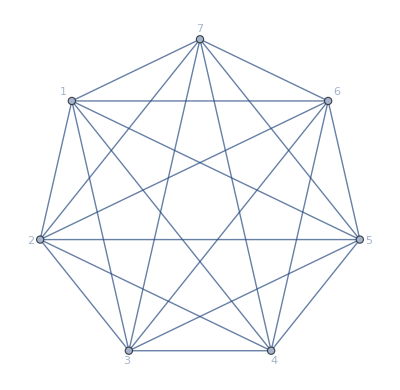
```mathematica
SelectDiscard[-Graphics-,OddQ]
```

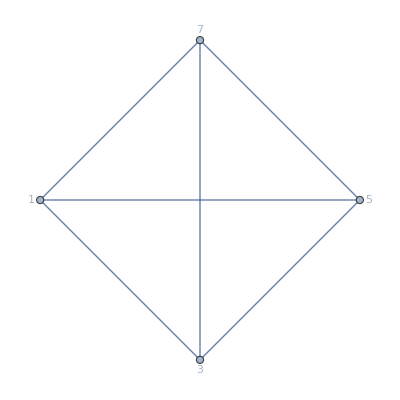
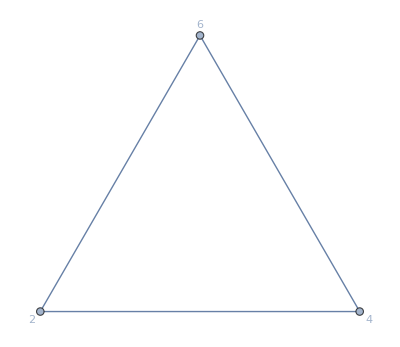

Maybe support this for images? It's kind of weird and arbitrary.

```mathematica
selDiscardImage[img_Image,func_]:=
Module[{mask1,mask2,i1,i2},
mask1=ImageApply[Boole@*TrueQ@*func,img];
mask2=ColorNegate@mask1;
i1=SetAlphaChannel[ImageMultiply[img,mask1],mask1];
i2=SetAlphaChannel[ImageMultiply[img,mask2],mask2];
{i1,i2}
];
```

```mathematica
selDiscardImage[-Graphics-,EuclideanDistance[#,{0,1,0}]<0.8&]
```

{-Graphics-,-Graphics-}

### Applications

Select numbers up to 100 that equal 1 modulo both 3 and 5:

```mathematica
SelectDiscard[Range[100],Mod[#,3]==1&&Mod[#,5]==1&]
```

{{1,16,31,46,61,76,91},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,92,93,94,95,96,97,98,99,100}}

Select 4-tuples that read the same in reverse:

```mathematica
SelectDiscard[Tuples[{a,b},4],#==Reverse[#]&]
```

{{{a,a,a,a},{a,b,b,a},{b,a,a,b},{b,b,b,b}},{{a,a,a,b},{a,a,b,a},{a,a,b,b},{a,b,a,a},{a,b,a,b},{a,b,b,b},{b,a,a,a},{b,a,b,a},{b,a,b,b},{b,b,a,a},{b,b,a,b},{b,b,b,a}}}

Select eigenvalues that lie within the unit circle:

```mathematica
SelectDiscard[Eigenvalues[RandomReal[1,{5,5}]],Abs[#]<1&]
```

{{0.507777+0.223889 ⅈ,0.507777-0.223889 ⅈ,-0.527869+0. ⅈ,-0.104087+0. ⅈ},{2.63854+0. ⅈ}}

Separate built-in Wolfram Language symbols based on whether their names contain less than 10 characters:

```mathematica
{short,long}=SelectDiscard[Names["System`*"],StringLength[#]<10&];
```

```mathematica
short//Short
```

{a,b,c,d,e,f,«1750»,$TraceOn,$Urgent,$Username,$UserName,$Version,\[SystemsModelDelay]}

```mathematica
long//Short
```

{AASTriangle,AbelianGroup,AbortKernels,«5745»,$WolframID,$WolframUUID}

Select numeric quantities from a product:

```mathematica
SelectDiscard[7 π^2 x^2 y^2,NumericQ]
```

{7 π^2,x^2 y^2}

### Properties & Relations

The lengths of list_1 and list_2 will always sum to the length of the original list:

```mathematica
SelectDiscard[Range[10],PrimeQ]
```

{{2,3,5,7},{1,4,6,8,9,10}}

When specifying a maximum, the second list can contain elements that satisfy the given condition:

```mathematica
SelectDiscard[Range[10],PrimeQ,2]
```

{{2,3},{5,7,1,4,6,8,9,10}}

SelectDiscard is similar to TakeDrop except it takes/drops elements using the given function:

```mathematica
list=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
SelectDiscard[list,LessEqualThan[4]]
```

{{1,2,3,4},{5,6,7,8,9,10}}

```mathematica
TakeDrop[list,4]
```

{{1,2,3,4},{5,6,7,8,9,10}}

For crit that always return True or False, SelectDiscard is very similar to GatherBy:

```mathematica
SelectDiscard[Range[10],OddQ]
```

{{1,3,5,7,9},{2,4,6,8,10}}

```mathematica
GatherBy[Range[10],OddQ]
```

{{1,3,5,7,9},{2,4,6,8,10}}

However, the first list returned by SelectDiscard always corresponds to elements e_i where crit[e_i] gives True:

```mathematica
SelectDiscard[Range[10],EvenQ]
```

{{2,4,6,8,10},{1,3,5,7,9}}

```mathematica
GatherBy[Range[10],EvenQ]
```

{{1,3,5,7,9},{2,4,6,8,10}}

Similar results can be obtained with GroupBy:

```mathematica
Lookup[GroupBy[Range[10],PrimeQ],{True,False},{}]
```

{{2,3,5,7},{1,4,6,8,9,10}}

However, SelectDiscard works on expressions with any head:

```mathematica
SelectDiscard[g[1,2,4,7,8],#>2&]
```

{g[4,7,8],g[1,2]}

GroupBy does not:

```mathematica
GroupBy[g[1,2,4,7,8],#>2&]
```

GroupBy::list1: The argument g[1,2,4,7,8] is not a valid list of Associations or rules or lists of rules.

GroupBy[g[1,2,4,7,8],#1>2&]

SelectDiscard always gives two lists:

```mathematica
SelectDiscard[{1,2,4,7,x,y},#>2&]
```

{{4,7},{1,2,x,y}}

```mathematica
SelectDiscard[Range[5],IntegerQ]
```

{{1,2,3,4,5},{}}

Compare with GatherBy and GroupBy:

```mathematica
GatherBy[{1,2,4,7,x,y},#>2&]
```

{{1,2},{4,7},{x},{y}}

```mathematica
GroupBy[{1,2,4,7,x,y},#>2&]
```

<|False→{1,2},True→{4,7},x>2→{x},y>2→{y}|>

```mathematica
GroupBy[Range[5],IntegerQ]
```

<|True→{1,2,3,4,5}|>

```mathematica
GatherBy[Range[5],IntegerQ]
```

{{1,2,3,4,5}}

Similar results can be obtained with a combination of Select and DeleteElements:

```mathematica
list={1,2,2,3,3,4};
```

```mathematica
SelectDiscard[list,EvenQ]
```

{{2,2,4},{1,3,3}}

```mathematica
With[{sel=Select[list,EvenQ]},{sel,DeleteElements[list,sel]}]
```

{{2,2,4},{1,3,3}}

SelectDiscard tends to perform better with large lists:

```mathematica
list=RandomInteger[100,10000];
```

```mathematica
First[RepeatedTiming[SelectDiscard[list,EvenQ]]]
```

0.00613686

```mathematica
First[RepeatedTiming[With[{sel=Select[list,EvenQ]},{sel,DeleteElements[list,sel]}]]]
```

0.400921

The first list returned by SelectDiscard[list,crit] is equivalent to what's returned by Select[list,crit]:

```mathematica
list={-2,0,1,3,3,x,y};
```

```mathematica
First[SelectDiscard[list,Positive]]===Select[list,Positive]
```

True

The second list is effectively equivalent to Select[list,Not@*TrueQ@*crit]:

```mathematica
Last[SelectDiscard[list,Positive]]===Select[list,Not@*TrueQ@*Positive]
```

True

### Possible Issues

When specifying a limit, the second list can contain elements e_i where crit[e_i] is True:

```mathematica
SelectDiscard[{1,2,4,7,6,2},EvenQ,2]
```

{{2,4},{6,2,1,7}}

## Source & Additional Information

### Contributed By

Richard Hennigan (Wolfram Research)

### Keywords

select

discard

select drop

select remove

gather

filter

choose elements

compress APL

criteria

deleting elements

discard list elements

elements

expressions

filtering lists

occurrence

lists

mu operator

picking elements lists

predicates

satisfying criterion

dget

subtotal

remove

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

Select

TakeDrop

GatherBy

GroupBy

Cases

DeleteCases

SelectFirst

### Related Resource Objects

Discard

SelectPositions

SelectAtLevel

Duplicates

### Source/Reference Citation

Source, reference or citation information

### Links

SelectDiscard | rhennigan/ResourceFunctions | GitHub

Tutorial: Selecting Parts of Expressions with Functions

Guide: Elements of Lists

Guide: Functional Programming

Guide: Function Composition & Operator Forms

Guide: List Manipulation

Fast Introduction for Programmers: Functionals & Operators

An Elementary Introduction to the Wolfram Language: Tests and Conditionals

An Elementary Introduction to the Wolfram Language: Expressions and Their Structure

An Elementary Introduction to the Wolfram Language: Datasets

NKS|Online

### Tests

#### Initialization

```mathematica
VerificationTest[
    SetOptions[ ResourceFunction[ "MessageFailure" ], "TestMode" -> True ],
    KeyValuePattern[ "TestMode" -> True ],
    SameTest -> MatchQ
]
```

#### Tests

##### Basic Examples

```mathematica
VerificationTest[
    SelectDiscard[ { 1, 2, 4, 7, 6, 2 }, EvenQ ],
    { { 2, 4, 6, 2 }, { 1, 7 } },
    TestID -> "BasicExamples-1"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ { 1, 2, 4, 7, 6, 2 }, #1 > 2 & ],
    { { 4, 7, 6 }, { 1, 2, 2 } },
    TestID -> "BasicExamples-2"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ { 1, 2, 4, 7, 6, 2 }, #1 > 2 &, 1 ],
    { { 4 }, { 7, 6, 1, 2, 2 } },
    TestID -> "BasicExamples-3"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ EvenQ ][ { 1, 2, 4, 7, 6, 2 } ],
    { { 2, 4, 6, 2 }, { 1, 7 } },
    TestID -> "BasicExamples-4"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ <| a -> 1, b -> 2, c -> 3, d -> 4 |>, #1 > 2 & ],
    { <| c -> 3, d -> 4 |>, <| a -> 1, b -> 2 |> },
    TestID -> "BasicExamples-5"
]
```

##### Scope

```mathematica
VerificationTest[
    SelectDiscard[ { 1, 2, 4, 7, x }, #1 > 2 & ],
    { { 4, 7 }, { 1, 2, x } },
    TestID -> "Scope-1"
]
```

```mathematica
VerificationTest[
    SelectDiscard[
        { { 1, y }, { 2, x }, { 3, x }, { 4, z }, { 5, x } },
        MemberQ[ #1, x ] &
    ],
    { { { 2, x }, { 3, x }, { 5, x } }, { { 1, y }, { 4, z } } },
    TestID -> "Scope-2"
]
```

```mathematica
VerificationTest[
    SelectDiscard[
        { { 1, y }, { 2, x }, { 3, x }, { 4, z }, { 5, x } },
        MemberQ[ #1, x ] &,
        2
    ],
    { { { 2, x }, { 3, x } }, { { 5, x }, { 1, y }, { 4, z } } },
    TestID -> "Scope-3"
]
```

```mathematica
VerificationTest[
    SelectDiscard[
        { { 1, y }, { 2, x }, { 3, x }, { 4, z }, { 5, x } },
        MemberQ[ #1, z ] &,
        2
    ],
    { { { 4, z } }, { { 1, y }, { 2, x }, { 3, x }, { 5, x } } },
    TestID -> "Scope-4"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ Range[ 10 ], GreaterThan[ 3 ] ],
    { { 4, 5, 6, 7, 8, 9, 10 }, { 1, 2, 3 } },
    TestID -> "Scope-5"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ GreaterThan[ 3 ] ][ Range[ 10 ] ],
    { { 4, 5, 6, 7, 8, 9, 10 }, { 1, 2, 3 } },
    TestID -> "Scope-6"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ Unevaluated[ 1 + 2 + 3 + 4 + 5 ], OddQ ],
    { 9, 6 },
    TestID -> "Scope-7"
]
```

##### Generalizations & Extensions

```mathematica
VerificationTest[
    SelectDiscard[ h[ 1, a, 2, b, 3 ], IntegerQ ],
    { h[ 1, 2, 3 ], h[ a, b ] },
    TestID -> "GeneralizationsAndExtensions-1"
]
```

```mathematica
VerificationTest[
    s = SparseArray @ Table[ 2^i -> i, { i, 0, 5 } ],
    _SparseArray? SparseArrayQ,
    SameTest -> MatchQ,
    TestID -> "GeneralizationsAndExtensions-2"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ s, EvenQ ],
    {
        SparseArray[ Automatic, { 29 }, 0, { 1, { { 0, 2 }, { { 3 }, { 14 } } }, { 2, 4 } } ],
        { 1, 3, 5 }
    },
    TestID -> "GeneralizationsAndExtensions-3"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ s, OddQ ],
    {
        { 1, 3, 5 },
        SparseArray[ Automatic, { 29 }, 0, { 1, { { 0, 2 }, { { 3 }, { 14 } } }, { 2, 4 } } ]
    },
    TestID -> "GeneralizationsAndExtensions-4"
]
```

```mathematica
VerificationTest[
    { g1, g2 } = SelectDiscard[ CompleteGraph[ 7 ], OddQ ],
    { _Graph? GraphQ, _Graph? GraphQ },
    SameTest -> MatchQ,
    TestID   -> "GeneralizationsAndExtensions-5"
]
```

```mathematica
VerificationTest[
    IsomorphicGraphQ[
        g1,
        Graph @ { 1 <-> 3, 1 <-> 5, 1 <-> 7, 3 <-> 5, 3 <-> 7, 5 <-> 7 }
    ],
    True,
    TestID -> "GeneralizationsAndExtensions-6"
]
```

```mathematica
VerificationTest[
    IsomorphicGraphQ[
        g2,
        Graph @ { 2 <-> 4, 2 <-> 6, 4 <-> 6 }
    ],
    True,
    TestID -> "GeneralizationsAndExtensions-7"
]
```

##### Applications

```mathematica
VerificationTest[
    SelectDiscard[ 7 * Pi^2 * x^2 * y^2, NumericQ ],
    { 7 * Pi^2, x^2 * y^2 },
    TestID -> "Applications-1"
]
```

##### Properties and Relations

```mathematica
VerificationTest[
    list = Range[ 10 ],
    { 1, 2, 3, 4, 5, 6, 7, 8, 9, 10 },
    TestID -> "PropertiesAndRelations-1"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ list, LessEqualThan[ 4 ] ],
    TakeDrop[ list, 4 ],
    TestID -> "PropertiesAndRelations-2"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ Range[ 10 ], OddQ ],
    { { 1, 3, 5, 7, 9 }, { 2, 4, 6, 8, 10 } },
    TestID -> "PropertiesAndRelations-3"
]
```

```mathematica
VerificationTest[
    GatherBy[ Range[ 10 ], OddQ ],
    { { 1, 3, 5, 7, 9 }, { 2, 4, 6, 8, 10 } },
    TestID -> "PropertiesAndRelations-4"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ Range[ 10 ], EvenQ ],
    { { 2, 4, 6, 8, 10 }, { 1, 3, 5, 7, 9 } },
    TestID -> "PropertiesAndRelations-5"
]
```

```mathematica
VerificationTest[
    GatherBy[ Range[ 10 ], EvenQ ],
    { { 1, 3, 5, 7, 9 }, { 2, 4, 6, 8, 10 } },
    TestID -> "PropertiesAndRelations-6"
]
```

```mathematica
VerificationTest[
    Lookup[ GroupBy[ Range[ 10 ], PrimeQ ], { True, False }, { } ],
    { { 2, 3, 5, 7 }, { 1, 4, 6, 8, 9, 10 } },
    TestID -> "PropertiesAndRelations-7"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ g[ 1, 2, 4, 7, 8 ], #1 > 2 & ],
    { g[ 4, 7, 8 ], g[ 1, 2 ] },
    TestID -> "PropertiesAndRelations-8"
]
```

```mathematica
VerificationTest[
    GroupBy[ g[ 1, 2, 4, 7, 8 ], #1 > 2 & ],
    HoldPattern @ GroupBy[ g[ 1, 2, 4, 7, 8 ], #1 > 2 & ],
    { GroupBy::list1 },
    SameTest -> MatchQ,
    TestID -> "PropertiesAndRelations-9"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ { 1, 2, 4, 7, x, y }, #1 > 2 & ],
    { { 4, 7 }, { 1, 2, x, y } },
    TestID -> "PropertiesAndRelations-10"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ Range[ 5 ], IntegerQ ],
    { { 1, 2, 3, 4, 5 }, { } },
    TestID -> "PropertiesAndRelations-11"
]
```

```mathematica
VerificationTest[
    GatherBy[ { 1, 2, 4, 7, x, y }, #1 > 2 & ],
    { { 1, 2 }, { 4, 7 }, { x }, { y } },
    TestID -> "PropertiesAndRelations-12"
]
```

```mathematica
VerificationTest[
    GroupBy[ { 1, 2, 4, 7, x, y }, #1 > 2 & ],
    <|
        False -> { 1, 2 },
        True  -> { 4, 7 },
        x > 2 -> { x },
        y > 2 -> { y }
    |>,
    TestID -> "PropertiesAndRelations-13"
]
```

```mathematica
VerificationTest[
    GroupBy[ Range[ 5 ], IntegerQ ],
    <| True -> { 1, 2, 3, 4, 5 } |>,
    TestID -> "PropertiesAndRelations-14"
]
```

```mathematica
VerificationTest[
    GatherBy[ Range[ 5 ], IntegerQ ],
    { { 1, 2, 3, 4, 5 } },
    TestID -> "PropertiesAndRelations-15"
]
```

```mathematica
VerificationTest[
    list = { 1, 2, 2, 3, 3, 4 },
    { 1, 2, 2, 3, 3, 4 },
    TestID -> "PropertiesAndRelations-16"
]
```

```mathematica
VerificationTest[
    SelectDiscard[ list, EvenQ ],
    { { 2, 2, 4 }, { 1, 3, 3 } },
    TestID -> "PropertiesAndRelations-17"
]
```

```mathematica
VerificationTest[
    With[ { sel = Select[ list, EvenQ ] },
        { sel, DeleteElements[ list, sel ] }
    ],
    { { 2, 2, 4 }, { 1, 3, 3 } },
    TestID -> "PropertiesAndRelations-18"
]
```

```mathematica
VerificationTest[
    list = { -2, 0, 1, 3, 3, x, y },
    { -2, 0, 1, 3, 3, x, y },
    TestID -> "PropertiesAndRelations-19"
]
```

```mathematica
VerificationTest[
    First @ SelectDiscard[ list, Positive ],
    Select[ list, Positive ],
    TestID -> "PropertiesAndRelations-20"
]
```

```mathematica
VerificationTest[
    Last @ SelectDiscard[ list, Positive ],
    Select[ list, Composition[ Not, TrueQ, Positive ] ],
    TestID -> "PropertiesAndRelations-21"
]
```

##### Possible Issues

##### Neat Examples

##### Error Cases

Argument count:

```mathematica
VerificationTest[
    SelectDiscard[ ],
    Failure[ "SelectDiscard::ArgumentCount", _ ],
    { SelectDiscard::ArgumentCount },
    SameTest -> MatchQ,
    TestID -> "ErrorCases-1"
]

VerificationTest[
    SelectDiscard[ { 1, 2, 3 }, OddQ, 1, 1 ],
    Failure[ "SelectDiscard::ArgumentCount", _ ],
    { SelectDiscard::ArgumentCount },
    SameTest -> MatchQ,
    TestID -> "ErrorCases-2"
]
```

Non-normal expression:

```mathematica
VerificationTest[
    SelectDiscard[ 1, crit ],
    Failure[ "SelectDiscard::Normal", _ ],
    { SelectDiscard::Normal },
    SameTest -> MatchQ,
    TestID   -> "ErrorCases-3"
]
```

Bad count spec:

```mathematica
VerificationTest[
    SelectDiscard[ { 1, 2, 3 }, OddQ, "x" ],
    Failure[ "SelectDiscard::Count", _ ],
    { SelectDiscard::Count },
    SameTest -> MatchQ,
    TestID   -> "ErrorCases-4"
]
```

#### Cleanup

```mathematica
VerificationTest[
    SetOptions[ ResourceFunction[ "MessageFailure" ], "TestMode" -> False ],
    KeyValuePattern[ "TestMode" -> False ],
    SameTest -> MatchQ
]
```

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.